```mathematica
(* visualise phylogenies and recombination gene presence/absence *)
(* there is no analysis here -- just visualisation. this pipeline is messy and we aim to smoothen it with ETE3 or phytools in future! *)
```

```mathematica
(* read presence/absence barcodes *)
```

```mathematica
barcodes = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/barcodes.txt", String];
```

```mathematica
(* read nodes and edges *)
```

```mathematica
l = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/commontree.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/commontree.txt-old.txt.padded-labels", String];
```

```mathematica
(* build graph and labels *)
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
blabels= bcodes = {};
For[i=2,i≤Length[barcodes],i++,
tmp = StringSplit[barcodes[[i]], " "];
AppendTo[blabels,StringSplit[tmp[[2]], "\""][[1]]<>" "<>StringSplit[tmp[[3]], "\""][[1]]];
AppendTo[bcodes, {ToExpression[tmp[[4]]], ToExpression[tmp[[5]]], ToExpression[tmp[[6]]], ToExpression[tmp[[7]]]}];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae", "Metazoa", "Anthozoa", "Placozoa", "Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Porifera"}
```

{Eukaryota,Fungi,Viridiplantae,Metazoa,Anthozoa,Placozoa,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Porifera}

```mathematica
offset[str_]:= If[str=="Porifera", {-0.2,0}, {0,0}]
```

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Style[Text[s[[vlabel]], vpos+offset[s[[vlabel]]], {-1,0},{0,1}], 12]],If[Length[Position[blabels, s[[vlabel]]]] ≠ 0, Table[If[bcodes[[Position[blabels, s[[vlabel]]][[1]][[1]]]][[i]]==1,{Black, Rectangle[vpos+{0,-0.05-0.025*i},vpos+{0,-0.05-0.025*i}+{0.05,0.02}]}], {i, 1, 4}]]};
```

Part::partw: Part 2485 of {Eukaryota,Rotosphaerida,ghost,ghost,ghost,ghost,ghost,Fonticula alba,Apusomonadidae,ghost,ghost,ghost,ghost,ghost,Thecamonas trahens,Cercozoa,ghost1,ghost1,ghost1,ghost1,ghost1,Bigelowiella natans,Filasterea,ghost1,ghost1,ghost1,ghost1,ghost1,Capsaspora owczarzaki,Choanoflagellata,Salpingoecidae,Salpingoeca,ghost2,ghost2,ghost2,Salpingoeca rosetta,Monosiga,ghost2,ghost2,ghost2,Monosiga brevicollis,Eustigmatophyceae,ghost2,ghost2,ghost2,ghost2,ghost3,Nannochloropsis gaditana,Ichthyosporea,ghost3,«2434»} does not exist.

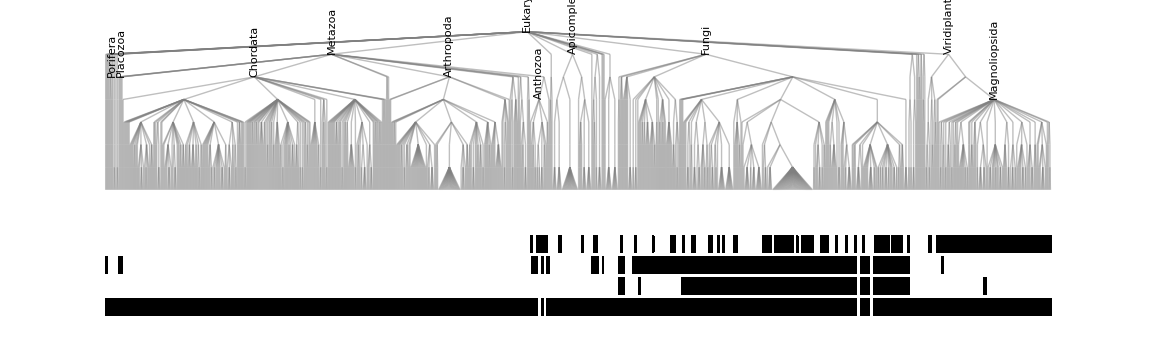

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.3]
```

```mathematica
(* the code below does the same thing for individual genes, and other subsets of interest *)
```

```mathematica
barcodes = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/barcodes.txt", String];
```

```mathematica
l = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/commontree-metazoa.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/commontree-metazoa.txt-old.txt.padded-labels", String];
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
blabels= bcodes = {};
For[i=2,i≤Length[barcodes],i++,
tmp = StringSplit[barcodes[[i]], " "];
AppendTo[blabels,StringSplit[tmp[[2]], "\""][[1]]<>" "<>StringSplit[tmp[[3]], "\""][[1]]];
AppendTo[bcodes, {ToExpression[tmp[[4]]], ToExpression[tmp[[5]]], ToExpression[tmp[[6]]], ToExpression[tmp[[7]]]}];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae", "Metazoa", "Anthozoa", "Placozoa", "Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda"}
```

{Eukaryota,Fungi,Viridiplantae,Metazoa,Anthozoa,Placozoa,Apicomplexa,Chordata,Magnoliopsida,Arthropoda}

```mathematica
offset[str_]:= If[str=="Porifera", {-0.2,0}, {0,0}]
```

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Text[s[[vlabel]], vpos+offset[s[[vlabel]]], {-1,0},{0,1}]],If[Length[Position[blabels, s[[vlabel]]]] ≠ 0, Table[{If[bcodes[[Position[blabels, s[[vlabel]]][[1]][[1]]]][[i]]==1,Black,White], Rectangle[vpos+{0,-0.05-0.025*i},vpos+{0,-0.05-0.025*i}+{0.05,0.02}]}, {i, 1, 4}]]};
```

Part::partw: Part 1553 of {Metazoa,Porifera,ghost,ghost,ghost,ghost,ghost,Amphimedon queenslandica,Priapulida,ghost,ghost,ghost,ghost,ghost,Priapulus caudatus,Placozoa,ghost1,ghost1,ghost1,ghost1,ghost1,Trichoplax adhaerens,Hemichordata,ghost1,ghost1,ghost1,ghost1,ghost1,Saccoglossus kowalevskii,Chordata,Cladistia,ghost2,ghost2,ghost2,ghost2,Erpetoichthys calabaricus,Mammalia,Dermoptera,ghost2,ghost2,ghost2,Galeopterus variegatus,Scandentia,ghost2,ghost2,ghost2,Tupaia chinensis,Chrysochloridae,ghost3,ghost3,«1502»} does not exist.

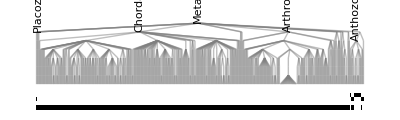

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.3]
```

```mathematica
l = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/msh1-blastx-tree.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/msh1-blastx-tree.txt-old.txt.padded-labels", String];
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae",  "Anthozoa", "Placozoa", "Porifera","Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Hexacorallia","Actiniaria","Antipatharia","Corallimorpharia","Scleractinia","Zoantharia","Octocorallia","Alcyonacea","Helioporacea","Pennatulacea","Ceriantharia","Penicillaria","Spirularia", "Porifera", "Actiniaria", "Basidiomycota", "Ascomycota"}
```

{Eukaryota,Fungi,Viridiplantae,Anthozoa,Placozoa,Porifera,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Hexacorallia,Actiniaria,Antipatharia,Corallimorpharia,Scleractinia,Zoantharia,Octocorallia,Alcyonacea,Helioporacea,Pennatulacea,Ceriantharia,Penicillaria,Spirularia,Porifera,Actiniaria,Basidiomycota,Ascomycota}

```mathematica
offset[str_]:= If[str=="Fungi", {-0.2,0}, {0,0}]
```

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Text[s[[vlabel]], vpos+offset[s[[vlabel]]], {-1,0},{0,1}]]};
```

Part::partw: Part 6759 of {Eukaryota,Vitrellaceae,ghost,ghost,ghost,ghost,ghost,ghost,ghost,Vitrella brassicaformis CCMP3155,Cryptophyceae,ghost,ghost,ghost,ghost1,ghost1,ghost1,ghost1,Guillardia theta CCMP2712,Bacillariophyta,Bacillariophyceae,Naviculales,ghost1,ghost1,ghost1,ghost1,ghost1,Fistulifera solaris,Bacillariales,Bacillariaceae,Fragilariopsis,ghost1,ghost2,ghost2,Fragilariopsis cylindrus CCMP1102,Pseudo-nitzschia,ghost2,ghost2,ghost2,Pseudo-nitzschia multistriata,Coscinodiscophyceae,Thalassiosira,Thalassiosira pseudonana,ghost2,ghost2,ghost2,ghost2,Thalassiosira pseudonana CCMP1335,ghost2,ghost3,«6708»} does not exist.

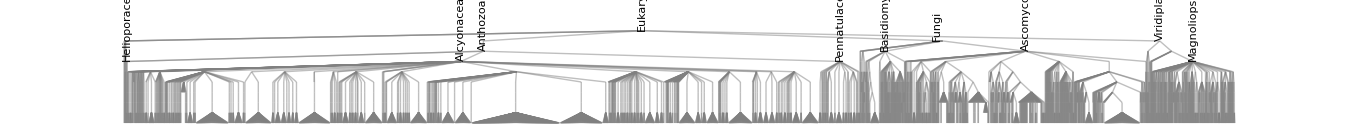

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.1]
```

Part::partw: Part 3929 of {Eukaryota,Fungi,ghost,ghost,ghost,ghost,ghost,ghost,Basidiobolus meristosporus CBS 931.73,Vitrellaceae,ghost,ghost,ghost,ghost,ghost1,ghost1,Vitrella brassicaformis CCMP3155,Cryptophyceae,ghost1,ghost1,ghost1,ghost1,ghost1,ghost1,Guillardia theta CCMP2712,Bacillariophyta,Bacillariophyceae,Naviculales,ghost1,ghost1,ghost2,ghost2,Fistulifera solaris,Bacillariales,Bacillariaceae,Fragilariopsis,ghost2,ghost2,Fragilariopsis cylindrus CCMP1102,Pseudo-nitzschia,ghost2,ghost2,Pseudo-nitzschia multistriata,Coscinodiscophyceae,Thalassiosira,Thalassiosira pseudonana,ghost2,ghost2,ghost2,Thalassiosira pseudonana CCMP1335,«3878»} does not exist.

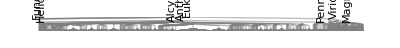

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.1]
```

```mathematica
l = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/mgm101-blastx-tree.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/mgm101-blastx-tree.txt-old.txt.padded-labels", String];
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae",  "Anthozoa", "Placozoa", "Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Porifera", "Ascomycota", "Basidiomycota", "Dictyosteliales", "Physariida", "Acytosteliales", "Heterolobosea", "Zoopagomycota", "Chytridiomycota","Cryptomycota" }
```

{Eukaryota,Fungi,Viridiplantae,Anthozoa,Placozoa,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Porifera,Ascomycota,Basidiomycota,Dictyosteliales,Physariida,Acytosteliales,Heterolobosea,Zoopagomycota,Chytridiomycota,Cryptomycota}

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae",  "Anthozoa", "Placozoa", "Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Porifera", "Ascomycota", "Basidiomycota", "Dictyosteliales" , "Physariida", "Mucoromycota", "Dothideomycetes","Eurotiomycetes", "Sordariomycetes", "Saccharomycetes", "Agaricomycetes" , "Microbotryomycetes", "Tremellomycetes", "Actiniaria"}
```

{Eukaryota,Fungi,Viridiplantae,Anthozoa,Placozoa,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Porifera,Ascomycota,Basidiomycota,Dictyosteliales,Physariida,Mucoromycota,Dothideomycetes,Eurotiomycetes,Sordariomycetes,Saccharomycetes,Agaricomycetes,Microbotryomycetes,Tremellomycetes,Actiniaria}

```mathematica
yoff = 0.1;
```

```mathematica
offset[str_]:= If[str=="Viridiplantae", {-0.1,yoff},If[str=="Porifera", {-0.1,0},If[str=="Placozoa", {0.,yoff},If[str=="Physariida", {0.25,yoff}, If[str=="Actiniaria", {0.1,yoff},If[str=="Dictyosteliales", {0.35,0},If[str=="Basidiomycota", {0.25,0},{0,0}]]]]] ]]
```

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Text[s[[vlabel]], vpos+offset[s[[vlabel]]], {-1,0},{0,1}]]};
```

Part::partw: Part 3479 of {Eukaryota,Discosea,ghost,ghost,ghost,ghost,ghost,ghost,ghost,Acanthamoeba castellanii str. Neff,Rotosphaerida,ghost,ghost,ghost,ghost1,ghost1,ghost1,ghost1,Fonticula alba,Jakobida,ghost1,ghost1,ghost1,ghost1,ghost1,ghost1,ghost2,Andalucia godoyi,Viridiplantae,Fagales,Betulaceae,ghost2,ghost2,ghost2,ghost2,ghost2,Carpinus fangiana,Fagaceae,ghost2,ghost2,ghost2,ghost2,ghost3,Quercus suber,Metazoa,Porifera,ghost3,ghost3,ghost3,ghost3,«3428»} does not exist.

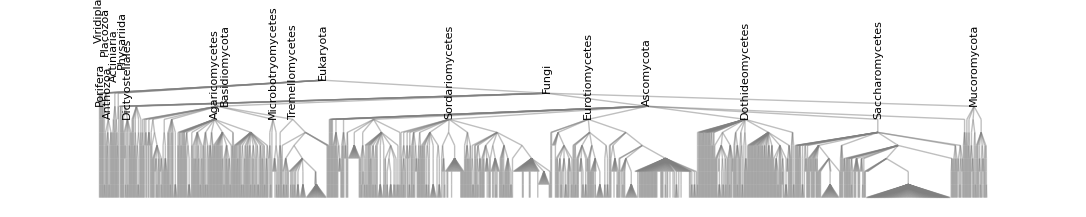

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.2]
```

```mathematica
l = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/mhr1-blastx-tree.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["~/Dropbox/EvoConBiO/WP3/Bioinf/News/mhr1-blastx-tree.txt-old.txt.padded-labels", String];
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae",  "Anthozoa", "Placozoa", "Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Porifera", "Ascomycota", "Basidiomycota",  "Basidiomycota", "Dictyosteliales" , "Physariida", "Mucoromycota", "Dothideomycetes","Eurotiomycetes", "Sordariomycetes", "Saccharomycetes", "Agaricomycetes" , "Microbotryomycetes", "Tremellomycetes"}
```

{Eukaryota,Fungi,Viridiplantae,Anthozoa,Placozoa,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Porifera,Ascomycota,Basidiomycota,Basidiomycota,Dictyosteliales,Physariida,Mucoromycota,Dothideomycetes,Eurotiomycetes,Sordariomycetes,Saccharomycetes,Agaricomycetes,Microbotryomycetes,Tremellomycetes}

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Text[s[[vlabel]], vpos, {-1,0},{0,1}]]};
```

Part::partw: Part 542 of {Ascomycota,Dothideomycetes,Zopfiaceae,ghost,ghost,ghost,ghost,ghost,Zopfia rhizophila CBS 207.26,Pleosporales,Didymosphaeriaceae,Bimuria,ghost,ghost,ghost,Bimuria novae-zelandiae CBS 107.79,Karstenula,ghost,ghost,ghost1,Karstenula rhodostoma CBS 690.94,Sporormiaceae,ghost1,ghost1,ghost1,ghost1,Sporormia fimetaria CBS 119925,Melanommataceae,ghost1,ghost1,ghost1,ghost1,Melanomma pulvis-pyrius CBS 109.77,Pleomassariaceae,ghost1,ghost2,ghost2,ghost2,Pleomassaria siparia CBS 279.74,Lophiotremataceae,ghost2,ghost2,ghost2,ghost2,Lophiotrema nucula,Gloniaceae,Cenococcum,ghost2,ghost2,ghost2,«491»} does not exist.

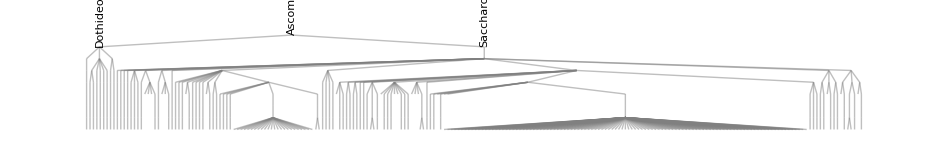

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.15]
```